```mathematica
SetDirectory[NotebookDirectory[]];
dataCu2p=Import["D:\\Experiments\\LEED_ARPES_Analysis\\Cu2p_1200eV.txt","Data"];
data1200eV=Import["D:\\Experiments\\LEED_ARPES_Analysis\\overview1200eV.txt","Data"];
data1300eV=Import["D:\\Experiments\\LEED_ARPES_Analysis\\Overview1300eV.txt","Data"];
```

```mathematica
dataCu2p[[1]]
```

{230,49.3434}

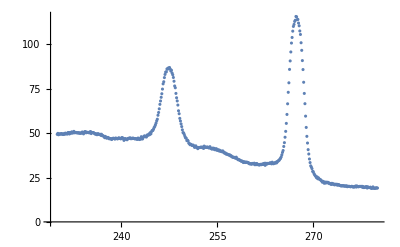

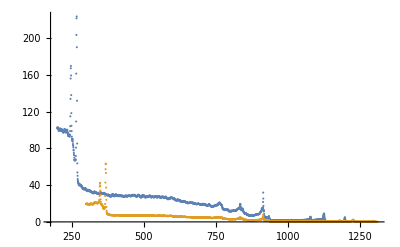

```mathematica
ListPlot[dataCu2p]
ListPlot[{data1200eV,data1300eV},PlotRange->All]
```

```mathematica
SurfaceState=Import["D:\\Experiments\\LEED_ARPES_Analysis\\surface_state.txt","Data"][[2;;-1,All]];
```

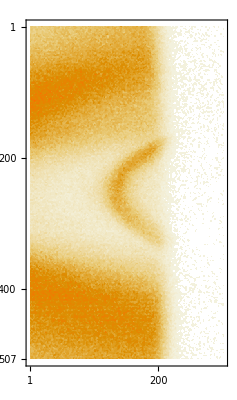

```mathematica
MatrixPlot[SurfaceState]
```

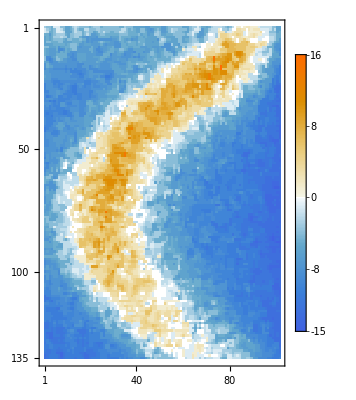

```mathematica
MatrixPlot[SurfaceState[[176;;310,110;;210]]-15,PlotLegends->Automatic]
```

```mathematica
band = SurfaceState[[180;;310,110;;210]]-15;
```

```mathematica
Length[band]
```

175

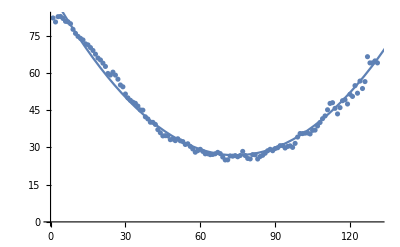

```mathematica
Show[ListPlot[Table[Sum[j*band[[i]][[j]]*HeavisideTheta[band[[i]][[j]]],{j,1,Length[band[[i]]]}]/Sum[band[[i]][[j]]*HeavisideTheta[band[[i]][[j]]],{j,1,Length[band[[i]]]}],{i,1,Length[band]}],PlotRange->All],Plot[92.82265010930641-1.7797524454703944 x+0.01200002765732349 x^2,{x,0,140}]]
```

```mathematica
Fit[Table[Sum[j*band[[i]][[j]]*HeavisideTheta[band[[i]][[j]]],{j,1,Length[band[[i]]]}]/Sum[band[[i]][[j]]*HeavisideTheta[band[[i]][[j]]],{j,1,Length[band[[i]]]}],{i,1,Length[band]}],{1,x,x^2},x]
```

92.8227-1.77975 x+0.012 x^2